## New Green’s function

```mathematica
ClearAll["`*"]
```

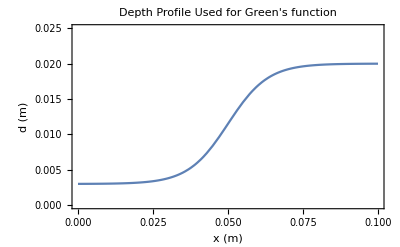

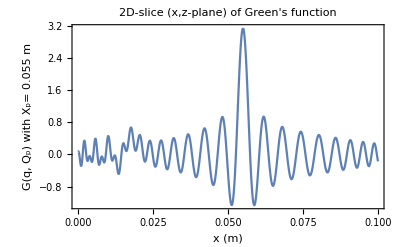

```mathematica
(*====================================================================*)
(*§1 Physical constants*)
(*====================================================================*)
σ=20.6*^-3;            (*surface tension (kg·s^-2)*)
ρ=949.;               (*density (kg·m^-3)*)
g=9.81;               (*gravity (m·s^-2)*)
l=Sqrt[σ/(ρ g)];       (*capillary length (m)*)
Ω=80 π;               (*forcing angular frequency*)

(*====================================================================*)
(*§2 User-defined geometry& flow ‒-FILL THESE IN*)
(*====================================================================*)

(*------------Depth profile d(x)-----------------------------------*)
dMax=20*10^-3;
dMin=3*10^-3;
χ=0.0133;
xm=0.05;
dFun[x_]:=(dMax+dMin)/2+(dMax-dMin)/2 Tanh[(x-xm)/χ]

(*Background-surface velocity v_B(x)-------------------------------*)
vFun[x_]:=0.001/dFun[x];

(*First and second spatial derivatives (supply analytic or numeric)*)
d1[x_?NumericQ]:=Evaluate[D[dFun[z],z]/. z->x];
d2[x_?NumericQ]:=Evaluate[D[dFun[z],{z,2}]/. z->x];
v1[x_?NumericQ]:=Evaluate[D[vFun[z],z]/. z->x];
v2[x_?NumericQ]:=Evaluate[D[vFun[z],{z,2}]/. z->x];

(*====================================================================*)
(*§3 Dispersion relation F(k,d,v)=0*)
(*====================================================================*)

F[k_,d_,v_]:=(Ω-v k)^2-g k (1+l^2 k^2) Tanh[k d];

(*partial derivatives------------------------------------------------*)
Fk[k_,d_,v_]:=D[F[k,d,v],k];
Fd[k_,d_,v_]:=D[F[k,d,v],d];
Fv[k_,d_,v_]:=D[F[k,d,v],v];

Fkk[k_,d_,v_]:=D[F[k,d,v],{k,2}];
Fkd[k_,d_,v_]:=D[F[k,d,v],k,d];
Fkv[k_,d_,v_]:=D[F[k,d,v],k,v];
Fdd[k_,d_,v_]:=D[F[k,d,v],{d,2}];
Fdv[k_,d_,v_]:=D[F[k,d,v],d,v];
Fvv[k_,d_,v_]:=D[F[k,d,v],{v,2}];

(*====================================================================*)
(*§4 Local root k(x)*)
(*====================================================================*)

kLocal[x_?NumericQ]:=Module[{d=dFun[x],v=vFun[x],k0},k0=Sqrt[Ω^2/g];(*deep-water initial guess*)k/. Quiet@FindRoot[F[k,d,v]==0,{k,k0},WorkingPrecision->20,AccuracyGoal->12,PrecisionGoal->12]];

(*====================================================================*)
(*§5 First and second spatial derivatives k'(x),k''(x)*)
(*====================================================================*)

hFD=1.*^-4;                       (*step size in metres*)

kPrime[x_?NumericQ]:=(kLocal[x+hFD]-kLocal[x-hFD])/(2 hFD);

kPrime2[x_?NumericQ]:=(kLocal[x+hFD]-2 kLocal[x]+kLocal[x-hFD])/(hFD^2);


(*====================================================================*)
(*§6 Implementing into Green's Function *)
(*====================================================================*)

kbar[x_?NumericQ]:=kLocal[x];
kprime[x_?NumericQ]:=kPrime[x];
kpp[x_?NumericQ]:=kPrime2[x];

Gfun[xp_?NumericQ,x_?NumericQ]:=Module[{dx=x-xp,r=Abs[x-xp],k0,kp,k2,th},{k0,kp,k2}={kbar[xp],kprime[xp],kpp[xp]};
If[!VectorQ[{k0,kp,k2},NumericQ],Return[$Failed]];
(*handle the singular self–point analytically*)If[r<10^-9,Return[N[1/Pi,15]]];
Quiet@NIntegrate[Cos[(k0+kp*dx*Cos[th]+0.5*k2*dx^2*Cos[th])*r*Sin[th]],{th,0.,Pi},(*stick to Automatic so every version of MMA understands it*)AccuracyGoal->8,PrecisionGoal->8,MaxRecursion->10]]


xp=0.055;
Plot[dFun[x],{x,0,0.1},PlotRange->{0,0.025},Frame->True,FrameLabel->{"x (m)","d (m)"},PlotLabel->"Depth Profile Used for Green's function"]
Plot[Gfun[xp,x],{x,0,0.1},Exclusions->{xp},Frame->True,FrameLabel->{"x (m)","G(q, Q_p) with X_p= 0.055 m"},PlotRange->All,PlotLabel->"2D-slice (x,z-plane) of Green's function"]
```